

```mathematica
Plot[X,{X,-2,2}]
```

```mathematica
Plot[x,{x,-2,2}]
```

-Graphics-

```mathematica
Integrate[Sin[x]Sin[x s],x]
```

(-s Cos[s x] Sin[x]+Cos[x] Sin[s x])/(-1+s^2)

```mathematica
Plot3D[
(-s Cos[s x] Sin[x]+Cos[x] Sin[s x])/(-1+s^2)
,{x,-2π,2π},{s,-2π,2π}]
```

-Graphics3D-

```mathematica
Plot3D[
(-s Cos[s x] Sin[x]+Cos[x] Sin[s x])/(-1+s^2)
,{x,-2π,2π},{s,-2π,2π}
,PlotRange->Full]
```

-Graphics3D-

```mathematica
Limit[Integrate[Sin[x]Sin[x s],{x,-a,a}],a->∞]
```

ConditionalExpression[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}], 1/(-1+s^2)∈ℝ&&s>0]

```mathematica
FullSimplify[
Limit[Integrate[Sin[x]Sin[x s],{x,-a,a}],a->∞]
,{x}∈Reals∧s∈
]
```

ConditionalExpression[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}], 1/(-1+s^2)∈ℝ]

```mathematica
FullSimplify[
Limit[Integrate[Sin[x]Sin[x s],{x,-a,a}],a->∞]
,{x}∈Reals∧s∈∧1/(s^2-1)∈Reals
]
```

Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]

```mathematica
Min[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]
```

Min[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]

```mathematica
Min[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]≤x≤Max[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]
```

Min[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]≤x≤Max[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]

```mathematica
Max[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]-Min[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]
```

Max[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]-Min[Interval[{Min[-2/(-1+s),2/(-1+s)],Max[-2/(-1+s),2/(-1+s)]}]]

```mathematica
LaplaceTransform[Exp[x],x,s]
```

1/(-1+s)

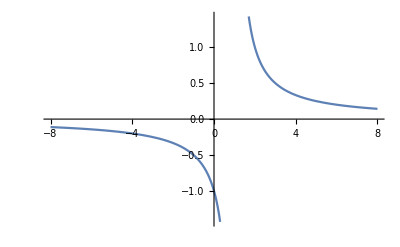

```mathematica
Plot[1/(-1+s),{s,-8,8}]
```

```mathematica
LaplaceTransform[Exp[-x],x,s]
```

1/(1+s)

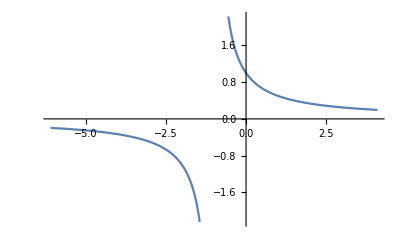

```mathematica
Plot[1/(1+s),{s,-6.1,4.1}]
```

```mathematica
LaplaceTransform[Sin[x],x,s]
```

1/(1+s^2)

```mathematica
LaplaceTransform[Sin[2x],x,s]
```

2/(4+s^2)

```mathematica
LaplaceTransform[Sin[-2x],x,s]
```

-2/(4+s^2)

```mathematica
LaplaceTransform[Sin[x^2],x,s]
```

1/2 √(π/2) (Cos[s^2/4] (1-2 FresnelC[s/(√(2 π))])+(1-2 FresnelS[s/(√(2 π))]) Sin[s^2/4])

```mathematica
FourierTransform[Sin[2x],x,s]
```

ⅈ √(π/2) DiracDelta[-2+s]-ⅈ √(π/2) DiracDelta[2+s]

```mathematica
FourierTransform[Cos[2x],x,s]
```

√(π/2) DiracDelta[-2+s]+√(π/2) DiracDelta[2+s]

```mathematica
FourierTransform[Tan[2x],x,s]
```

$Aborted